```mathematica
Clear["Global`*"]
```

```mathematica
ep=0;a=1;t=0.25;e=ep+1/2-1/2Sqrt[Cos[k a/2]^2+1];
```

```mathematica
h={{ep+1,t(1+Exp[-I k a])},{t(1+Exp[I k a]),ep}};
```

```mathematica
eigVector=Eigenvectors[h]
```

{{(2. ⅇ^((0.-1. ⅈ) k) (1. ⅇ^((0.+1. ⅈ) k)-1. √(0.25 ⅇ^((0.+1. ⅈ) k)+1.5 ⅇ^((0.+2. ⅈ) k)+0.25 ⅇ^((0.+3. ⅈ) k))))/(1.+ⅇ^((0.+1. ⅈ) k)),1.},{(2. ⅇ^((0.-1. ⅈ) k) (1. ⅇ^((0.+1. ⅈ) k)+1. √(0.25 ⅇ^((0.+1. ⅈ) k)+1.5 ⅇ^((0.+2. ⅈ) k)+0.25 ⅇ^((0.+3. ⅈ) k))))/(1.+ⅇ^((0.+1. ⅈ) k)),1.}}

```mathematica
eigVec1=eigVector[[1]];eigVec2=eigVector[[2]];
```

```mathematica
eigVec1=eigVec1/Sqrt[eigVec1[[1]]^2+eigVec1[[2]]^2](*Normalized eigenvector*);
eigVec2=eigVec2/Sqrt[eigVec2[[1]]^2+eigVec2[[2]]^2];
```

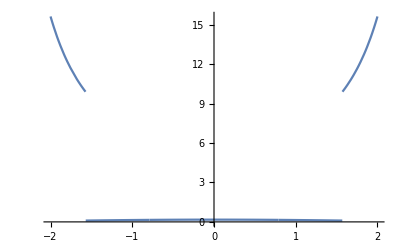

```mathematica
Plot[Conjugate[eigVec1[[1]]]eigVec1[[1]]/(Conjugate[eigVec1[[2]]]eigVec1[[2]])//Simplify,{k,-2,2}]
```

```mathematica
g=-2/Pi 16e/Sqrt[1-(8e^2-3)^2];
```

```mathematica
Plot[g*Assuming[k∈Reals,FullSimplify[Dot[Conjugate[eigVec2],eigVec2]]],{k,-2,2}]
```

-Graphics-

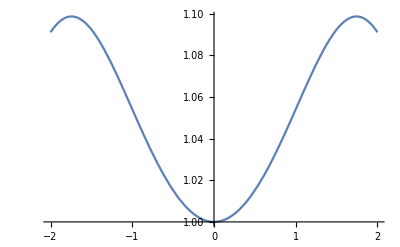

```mathematica
Plot[Assuming[k∈Reals,FullSimplify[Dot[Conjugate[eigVec2],eigVec2]]],{k,-2,2}]
```

```mathematica
g
```

-(32 (1/2-1/2 √(1+Cos[k/2]^2)))/(π √(1-(-3+8 (1/2-1/2 √(1+Cos[k/2]^2))^2)^2))

```mathematica
Simplify[-(32 (1/2-1/2 √(1+Cos[k/2]^2)))/(π √(1-(-3+8 (1/2-1/2 √(1+Cos[k/2]^2))^2)^2))]
```

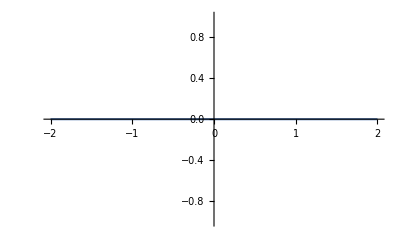

```mathematica
Plot[(8 (-2+√2 √(3+Cos[k])))/(π √(1-(2+Cos[k]-2 √2 √(3+Cos[k]))^2))//Re,{k,-2,2}]
```

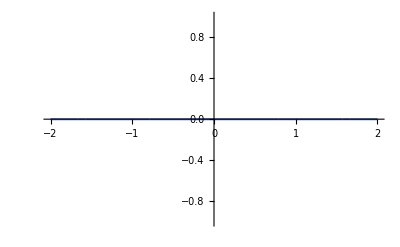

```mathematica
Plot[Re[Conjugate[eigVec1[[1]]]eigVec1[[1]]*g],{k,-2,2}]
```